```mathematica
y = {0.0008528232574462891, 0.005552530288696289, 0.0409548282623291, 0.2563445568084717, 1.7722728252410889, 12.37286901473999, 86.65874314308167, 605.7122931480408}
```

```mathematica
{0.0008528232574462891,0.005552530288696289,0.0409548282623291,0.2563445568084717,1.7722728252410889,12.37286901473999,86.65874314308167,605.7122931480408}

data = Table[{2 ^ i, y[[i - 1]]}, {i, 2, 9}]
```

{0.000852823,0.00555253,0.0409548,0.256345,1.77227,12.3729,86.6587,605.712}

{{4,0.000852823},{8,0.00555253},{16,0.0409548},{32,0.256345},{64,1.77227},{128,12.3729},{256,86.6587},{512,605.712}}

```mathematica
FindFormula[data, g]
```

0.0000157154 g^2.8

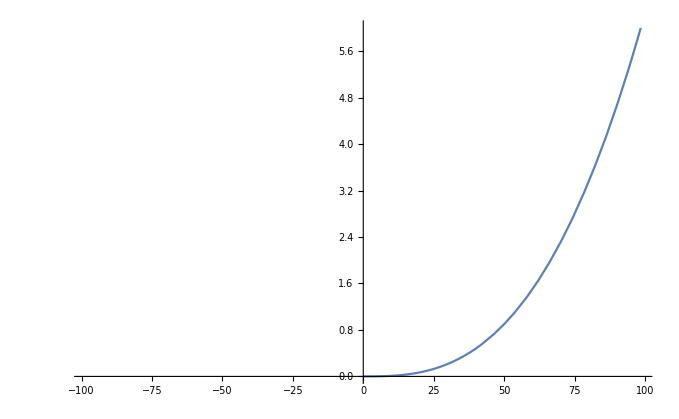

```mathematica
Plot[0.000015715399541592788 g^2.8,{g,-98.51655636188096,98.51655636188096}]
```